```mathematica
(* This notebook takes as input user and outputs the optimal spending schedule given AI timelines*)
(* User inputs:  *)
(* Time points t_i for AI timelines*)
time = {0,10,20,80};
(*AI timelines: probabity of AI by time t*)
pAI = {0,0.1,0.5};
(* Delta final (constante rate of transition to AGI after t final)*) 
δF :=0.001;
(* Delta initial*)
δ0 := 0.001;
parameters = { r->0.05,B->100,η->2};
```

```mathematica
(* Define function: probabity of no AI at time t[i+1] given no AI at time t[i] *)
(* TODO: Code return message if p[[i+1]]<p[[i]] *)
pTransition[pAI_, time_]:=Module[{ x,i, p = pAI, t=time},
x=ConstantArray[0, Length[pAI]-1];
	For[i=1, i<= Length[pAI]-1, i++, 
		x[[i]]=(1-p[[i+1]])/(1-p[[i]]);];
x]
```

```mathematica
(* Define function: δ as a sequence of affine function*)
δAff[δF_,time_]  :=  Module[{n},
(* Write δ as piecewise affine*)
n= Length[time]-1;
	For[i=1, i<= n,i++,
	δ[i]= a[i]+b[i]*t;  
		 ];
(* After t>=tF δ is constant *)
δ[Length[time]]= δF;
δ]
```

```mathematica
(* Function: Compute δ coefficients using continuity of δ at the boundary *)
δSol[δ_,δF_,δ0_, pT_, time_] := Module[{δInt, n= Length[time]-1},
(* Compute δInt *)
For[i=1, i<= n, i++,
δInt[i]=Integrate[δ[i], {t, time[[i]],time[[i+1]]}] ;];
(*Initialise recurrence*)
sol[1]=NSolve[{(δ[1]/.t->time[[1]])==δ0,δInt[1]== -Log[pT[[1]]]},{a[1],b[1]}];
(* Loop over boundary conditions *) 
For[i=2, i<= n, i++, sol[i]= NSolve[{(δ[i]/.t->time[[i]])==((δ[i-1]/.t->time[[i]])/.sol[i-1]), δInt[i]== -Log[pT[[i]]]},{a[i],b[i]}]];
(*Return solutions of affine recurrence*)
δS[1]=(δ[1]/.sol[1]);
(*for compatibility*)
δS[1]=δS[1][[1]];
δS[n+1]=δF;
For[i=2, i<= n, i++,
δS[i]=(δ[i]/.sol[i][[1]]);];
δS]
```

```mathematica
(* Function: Construct piecewise function *)
δPiece[δ_,time_] := Module[{δGraph, n = Length[time]-1},
δGraph = ConstantArray[t,{Length[time]-1,2 }];
For[i=1, i<=n,i++,δGraph[[i]][[1]] = δ[i]; δGraph[[i]][[2]]= time[[i]]<=t<=time[[i+1]]];
δP= Piecewise[δGraph, δ[Length[time]]];
δP]
```

```mathematica
(* Function: Compute probability of no AI at time t *)
pA[δP_]:=Module[{p,δInt},
δInt = Integrate[δP/.t->τ,{τ,0,t},Assumptions->0<=t]//FullSimplify ;
p = Exp[-δInt];
p]
```

```mathematica
(* Compute optiml spending schedule xStar by solving transversality condition. TODO Debug function *)
optimalSpending[pA_,δP_, parameters_, time_]:=Module[{xS, p,δ, zI, zF,z, cT},
(* From minimising hamiltonian w.r.t x *)
xS = ((c ⅇ^(-r t))/(p δ))^(-1/η);
xS  = xS/.p->pA/.δ->δP;
(* Solve transversality condition *)
$Assumptions = t∈Reals;
zI = NIntegrate[(xS*Exp[-r*t])/.parameters/.c->1,{t,0,time[[n]]}]/.parameters;
zF =NIntegrate[(xS*Exp[-r*t])/.t->τ/.parameters/.c->1, {τ,time[[n]],Infinity}] ;
z = B-c^(-1/η)*zI - c^(-1/η)*zF;
z = z/.parameters;
cT= NSolveValues[z ==0, c][[1]];
cT = Sqrt[Abs[cT]];
xS = xS/.c->cT;
xS]
```

```mathematica
pT = pTransition[pAI, time];
δ = δAff[δF,time];
δS = δSol[δ,δF,δ0, pT, time];
δP = δPiece[δS,time];
pTAI = pA[δP];
```

```mathematica
δS[4]/.t->time[[3]]
```

0.001

```mathematica
δS[1]=(δ[1]/.sol[1]);
```

```mathematica
δS[1][[1]]
```

0.001+0.00093225 t

sol[2]

```mathematica
δS[3]
```

a[3]+t b[3]/.{}⟦1⟧

```mathematica
xStar = optimalSpending[pTAI,δP,  parameters, time]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.17166}. NIntegrate obtained 3.36521-0.161208 ⅈ and 3.86463×10^-6 for the integral and error estimates.

0.0339444^(-1/η) (ⅇ^(-r t+(Piecewise[{{0., t≤0}, {1.60164+0.0001 t, t>78.}, {-1.13779+(0.0703417-0.000450267 t) t, 33.<t≤78.}, {(-0.00619675+0.000980178 t) t, 0.<t≤14.}, {-0.0921767+(0.00697135+0.000509889 t) t, True}}]))/Piecewise[{{-0.00619675+0.00196036 t, 0≤t≤14}, {0.00697135+0.00101978 t, 14≤t≤33}, {0.0703417-0.000900534 t, 33≤t≤78}, {0.0001, True}}])^(-1/η)

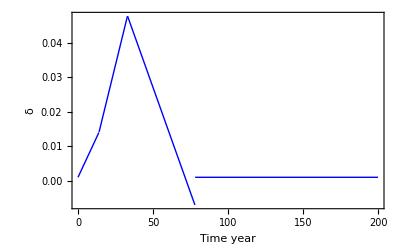

```mathematica
(*Plot instantaneous rate of transition to AI (Problem: some negative values!)*)
Plot[δP,{t,0,200}, Frame->True, FrameLabel->{Time (year), δ}, LabelStyle->{FontSize->18,FontFamily->"Times", ,Black,Bold}, PlotStyle->{Blue,Thick}]
```

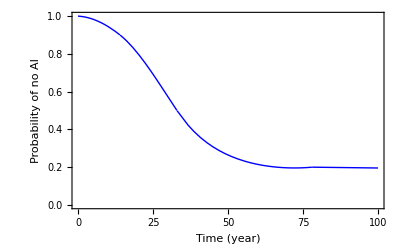

```mathematica
(*Plot probability of no AI over the next 100 years given timelines*)
Plot[pTAI, {t,0,100},PlotRange->{{0,100},{0,1}}, Frame->True, FrameLabel->{"Time (year)", "Probability of no AI"} ,LabelStyle->{FontSize->18,FontFamily->"Times", ,Black,Bold}, PlotStyle->{Blue,Thick}]
```

```mathematica
(*Compute endowment mStar when following optimal spending schedule xStar*)
mDot = r*m - xStar;
mStar = NDSolveValue[{m'[t]==(mDot/.m->m[t]/.parameters),m[0]==(B/.parameters)}, m[t],{t,0,200}]
```

InterpolatingFunction[…][t]

```mathematica
(*Assign user parameters to mDot*)
(mDot/.m->m[t]/.parameters)
```

0.05 m[t]-5.4277/(√(ⅇ^(-0.05 t+(Piecewise[{{0., t≤0}, {1.60164+0.0001 t, t>78.}, {-1.13779+(0.0703417-0.000450267 t) t, 33.<t≤78.}, {(-0.00619675+0.000980178 t) t, 0.<t≤14.}, {-0.0921767+(0.00697135+0.000509889 t) t, True}}]))/Piecewise[{{-0.00619675+0.00196036 t, 0≤t≤14}, {0.00697135+0.00101978 t, 14≤t≤33}, {0.0703417-0.000900534 t, 33≤t≤78}, {0.0001, True}}]))

```mathematica
InterpolatingFunction[…][t]
```

InterpolatingFunction[…][t]

```mathematica
(*Plot endowment*)
Plot[m[t]/.m[t]->mStar/.parameters, {t,0,100}, Frame->True, FrameLabel->{"Time (year)", "Money in % of initial endowment"}, LabelStyle->{FontSize->18}, PlotStyle->{Blue,Thick}]
```

-Graphics-

```mathematica
(* Plot spending schedule as fraction of endowment *)
Plot[((xStar/m[t]*100)/.m[t]->mStar/. parameters), {t,0,100}, PlotRange->{{0,100},{0,5}},Frame->True, FrameLabel->{"Time (year)", "Spending schedule (% of endowment)"}, PlotStyle->{Blue,Thick}, LabelStyle->{FontSize->18}]
```

-Graphics-